# Universality in Multiway Cellular Automaton

## Universality in regular CA’s

Threshold for universality is two color, two neighbor (rule 110)

Can emulate any Turing machine

Proved by explicit construction

Intuitively, universality requires localized structures but low repetition

## Universality in multiway systems

Must be able to emulate any computation

Computation may require a bounded amount of computation for encoding and decoding

Possible definitions for universality of a class of multiway system:

For any computation, there is a corresponding branch of the state evolution for some multiway system with some initial condition

There must be a multiway system that results in the same halting / looping state as the result of any computation

For any computation, a corresponding branch in the multiway graph can be found in a bounded amount of computation

There must be some event selection function and initial condition that results in every possible computation

There is always some such system with a causal graph isomorphic to that of any other computation

Methods for finding universal multiway CA’s:

Find a rule with one path through the states graph corresponding to a universal singleway CA

Construct an event selection function that results in this evolution

Can be exactly the emulated computation or include extra intermediate steps

Construct the causal graph of every elementary multiway CA for some small tape size and match with the corresponding causal graph of rule 110

Continue the evolution and see if the causal graph still matches

## Testing

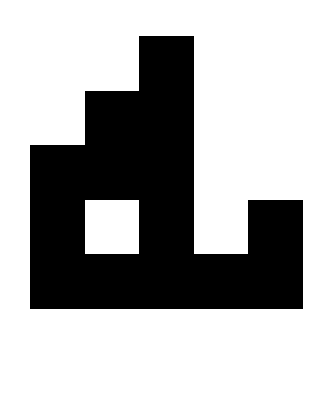

```mathematica
ArrayPlot@CellularAutomaton[110,CenterArray[1,5],5]
```

To exactly emulate this computation, the multiway system must be confluent with one end state (all white) from center black cell init

```mathematica
multi=ResourceFunction["MultiwaySystem"]
```

```mathematica
getStatesGraph[caRules_,rowSize_]:=ResourceFunction["MultiwaySystem"][CellularAutomaton[caRules],
	Tuples[{0,1},rowSize],1,"StatesGraph",ImageSize->Medium,
	"StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->30],#1,#3]&)]
confluentQ[graph_]:=AllTrue[WeaklyConnectedGraphComponents[graph],
	Function[cc,AnyTrue[VertexList[cc],ContainsExactly[VertexInComponent[cc,#],VertexList[cc]]&]]]
confluentStates[graph_]:=Function[cc,Select[VertexList[cc],
	ContainsExactly[VertexInComponent[cc,#],VertexList[cc]]&]]/@WeaklyConnectedGraphComponents[graph]
totalConfluentQ[graph_]:=CompleteGraphQ[TransitiveClosureGraph[graph]]
getSystemInfo[caRules_,rowSize_]:=With[{statesGraph=getStatesGraph[caRules,rowSize]},<|
	"rules"->caRules,"rowSize"->rowSize,
	"statesGraph"->statesGraph,
	"confluentQ"->confluentQ[statesGraph],
	"totalConfluentQ"->totalConfluentQ[statesGraph],
	"confluentStates"->Length[Flatten[confluentStates@statesGraph,1]]
	|>]
```

```mathematica
states=getStatesGraph[110,5]
```

-Graphics-

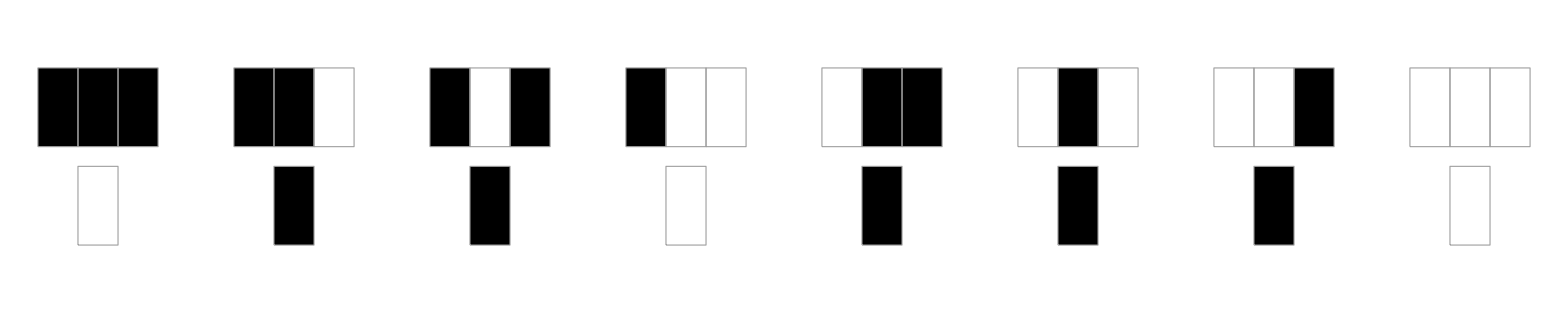

```mathematica
RulePlot@CellularAutomaton[110]
```

```mathematica
multi[CellularAutomaton[110],{1,0,1,1,0,1,0,0,1},1,"StatesGraph","StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->30],#1,#3]&)]
```

-Graphics-

So for this type of multiway system (apply one possible rule replacement at one possible position), the multiway version of a system doesn’t have to emulate its singleway behavior because performing a rule replacement at one location can change the possible next replacements, so you can’t necessarily repeat the same replacement to get the same transition as applying it everywhere at once.

If I search for any system that has a path corresponding to the rule 110 evolution, I’ll get all the totally confluent rules, which isn’t particularly useful. Maybe some of these could have an event selection function that could correspond to the singleway evolution?

Maybe looking for an isomorphic causal graph is a better approach?

I can't find any causal graphs of singleway automata and it's not clear if they would be useful. I could instead try to find a multiway CA causal graph isomorphic to a mobile automaton causal graph, but a mobile CA is effectively an extremely special case of a multiway CA and it may be difficult to find causal graph structures that line up perfectly. Maybe I could look for a path through the multiway causal graph corresponding to a universal mobile CA causal graph and look from there.

```mathematica
init=CenterArray[1,5];
steps=5;
```

```mathematica
Column@Manipulate[Framed@Labeled[LayeredGraphPlot[c=SimpleGraph@multi[CellularAutomaton[rule],init,steps,"CausalGraphStructure",ImageSize->Large]],Row[{Text@rule,confluentQ[g=multi[CellularAutomaton[rule],init,steps,"StatesGraph"]],totalConfluentQ@g,CompleteGraphQ@TransitiveClosureGraph@c}," "]],{rule,1,255,1}]
```

Column[]